## Configuration

```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];


SetOptions[Plot,LabelStyle->Directive[Background->White]];
```

Notebook load complete.

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$Assumptions=0<eps<1/10 && 0<M<Q && 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>0&&muMS>0&&1/3>tau>0&&0<qhatp<1&&0<qhatm<1&&xi>0&&nu>0&&muPrime>0&&nuPrime>0&&mu1>0;

waveZ=(alphabar/2)(1/eps-LM-1/2)

ansQCD=-2 zeta2 ᾱ+(ᾱ)/(2 ϵ)-2 ᾱ-1/2 Lis^2 ᾱ+(3 Lis ᾱ)/2+Lis LM ᾱ-(LM^2 ᾱ)/2-2 LM ᾱ-waveZ/.Lis->LQ-I*Pi//Expand
```

1/2 ᾱ (-LM+1/ϵ-1/2)

-2 ζ_2 ᾱ+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-(7 ᾱ)/4-1/2 LM^2 ᾱ-ⅈ π LM ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ^2 ᾱ)/2+(3 LQ ᾱ)/2+ⅈ π LQ ᾱ

```mathematica
ansQCD/.LQ->L+LM/.Pi^2->6zeta2//Expand
%*2//Expand
(%/.L->Li+I*Pi//Expand)/.Pi^2->6zeta2
```

ζ_2 ᾱ-3/2 ⅈ π ᾱ-(7 ᾱ)/4-1/2 L^2 ᾱ+ⅈ π L ᾱ+(3 L ᾱ)/2

2 ζ_2 ᾱ-3 ⅈ π ᾱ-(7 ᾱ)/2+L^2 (-ᾱ)+2 ⅈ π L ᾱ+3 L ᾱ

-4 ζ_2 ᾱ-(7 ᾱ)/2+Li^2 (-ᾱ)+3 Li ᾱ

### Canonical Way

```mathematica
(* the following from Simon and Ray's paper, eqs. 30-32 *)
igrandN=-(1-km/p1m)^(1-eps)/km
igrandNbar=DiracDelta[km-1]/(1-eps)+(p2p/M^2)*(-1+(-km*p2p/M^2)^-eps)/(1+p2p*km/M^2)//Expand
igrandOver=-1/km

(* do the well-defined integral -- the one with (-kp*p2p)^-eps in the numerator -- by hand. See below *)
igrandNbar=igrandNbar/.(-km*p2p/M^2)^(-eps)->M^2*(1+km*p2p/M^2)*DiracDelta[km-1]*(Pi*(-1/(1-I*delta))^(-eps)Csc[Pi*eps])/p2p


(*

(* here we have the 1-I*delta because the Feynman pole prescription tells us that in 1/(k^2-M^2), M^2->M^2-I*0 *)
 intEasy=Integrate[(-z/(1-I*delta))^-eps/(1+z),{z,0,Infinity}]

(-1/(1-I*delta))^(-eps)
%//FullSimplify
Series[%,{eps,0,1}]
Series[%,{delta,0,0}]//Normal


(-1-I*delta)^(-eps)
%//FullSimplify
Series[%,{eps,0,1}]
Series[%,{delta,0,0}]//Normal

*)
```

-((1-k^-/p_1^-)^(1-ϵ))/k^-

(k^--1)/(1-ϵ)+(p_2^+ (-(k^- p_2^+)/M^2)^-ϵ)/(M^2 ((k^- p_2^+)/M^2+1))-p_2^+/(M^2 ((k^- p_2^+)/M^2+1))

-1/k^-

π (-1/(1-ⅈ δ))^-ϵ k^--1 csc(π ϵ)+(k^--1)/(1-ϵ)-p_2^+/(M^2 ((k^- p_2^+)/M^2+1))

```mathematica
(* from 0 to p1m *)
igrandN+igrandNbar-igrandOver/.DiracDelta[_]->0
intLower=Integrate[%,{km,0,p1m}]
Series[intLower,{eps,0,1}]//Normal
```

-p_2^+/(M^2 ((k^- p_2^+)/M^2+1))-((1-k^-/p_1^-)^(1-ϵ))/k^-+1/k^-

-log((p_2^+ p_1^-)/M^2+1)+1/(1-ϵ)+01-ϵ+ℽ

-log((p_2^+ p_1^-)/M^2+1)+(1-π^2/6) ϵ+1

```mathematica
(* from p1m to infinity *)
igrandNbar-igrandOver/.DiracDelta[_]->0
intUpper=Integrate[%,{km,p1m,Infinity}]
```

1/k^--p_2^+/(M^2 ((k^- p_2^+)/M^2+1))

log(M^2/(p_2^+ p_1^-)+1)

```mathematica
prefac=alphabar(muMS^2Exp[EulerGamma]/(M^2))^(eps)Gamma[eps]
igrandTotal=prefac*(   SeriesCoefficient[igrandN+igrandNbar-igrandOver,{DiracDelta[_],0,1}]+intLower+intUpper   )

igrandTotal2=Series[%,{eps,0,0}]//Normal
igrandTotal3=Series[%,{delta,0,0}]//Normal
igrandTotal3=Series[%,{M,0,0}]//Normal
%/.Log[M]->LM/2+Log[muMS]/.Log[p1m*p2p]->LQ+2Log[muMS]
%-waveZ//Expand
ansUsual=%/.Pi^2->6zeta2//FullSimplify


SeriesCoefficient[ansQCD-ansUsual,{eps,0,0}]//Expand
Series[(1+ansQCD)/(1+ansUsual),{alphabar,0,1}]//Normal//Expand
c2Usual=(%-1)/alphabar//Expand
```

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ (π (-ⅈ/(δ+ⅈ))^-ϵ csc(π ϵ)+log(M^2/(p_2^+ p_1^-)+1)-log((p_2^+ p_1^-)/M^2+1)+2/(1-ϵ)+01-ϵ+ℽ)

(ᾱ)/ϵ^2+(ᾱ (-log(-ⅈ/(δ+ⅈ))+log(μ_OverBar[MS]^2/M^2)+log(M^2/(p_2^+ p_1^-)+1)-log((p_2^+ p_1^-)/M^2+1)+2))/ϵ+1/12 ᾱ (6 log^2(-ⅈ/(δ+ⅈ))+12 log(M^2/(p_2^+ p_1^-)+1) log(μ_OverBar[MS]^2/M^2)-12 log((p_2^+ p_1^-)/M^2+1) log(μ_OverBar[MS]^2/M^2)-12 log(-ⅈ/(δ+ⅈ)) log(μ_OverBar[MS]^2/M^2)+6 log^2(μ_OverBar[MS]^2/M^2)+24 log(μ_OverBar[MS]^2/M^2)+π^2+24)

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ+ᾱ log(M^2/(p_2^+ p_1^-)+1) log(μ_OverBar[MS]^2/M^2)-ᾱ log((p_2^+ p_1^-)/M^2+1) log(μ_OverBar[MS]^2/M^2)+(ᾱ log(μ_OverBar[MS]^2/M^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2/M^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2/M^2)+2 ᾱ log(μ_OverBar[MS]^2/M^2)+(ᾱ log(M^2/(p_2^+ p_1^-)+1))/ϵ-(ᾱ log((p_2^+ p_1^-)/M^2+1))/ϵ

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ-2 ᾱ log^2(M)-2 ⅈ π ᾱ log(M)-4 ᾱ log(M)+2 ᾱ log(M) log(p_2^+ p_1^-)-ᾱ log(p_2^+ p_1^-) log(μ_OverBar[MS]^2)+(ᾱ log(μ_OverBar[MS]^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)-(ᾱ log(p_2^+ p_1^-))/ϵ

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ+2 ᾱ (LM/2+log(μ_OverBar[MS])) (LQ+2 log(μ_OverBar[MS]))-2 ᾱ (LM/2+log(μ_OverBar[MS]))^2-2 ⅈ π ᾱ (LM/2+log(μ_OverBar[MS]))-4 ᾱ (LM/2+log(μ_OverBar[MS]))-(ᾱ (LQ+2 log(μ_OverBar[MS])))/ϵ-ᾱ log(μ_OverBar[MS]^2) (LQ+2 log(μ_OverBar[MS]))+(ᾱ log(μ_OverBar[MS]^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(3 ᾱ)/(2 ϵ)-(5 π^2 ᾱ)/12+(9 ᾱ)/4-1/2 LM^2 ᾱ-ⅈ π LM ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ ᾱ)/ϵ+2 LQ ᾱ log(μ_OverBar[MS])-LQ ᾱ log(μ_OverBar[MS]^2)-(2 ᾱ log(μ_OverBar[MS]))/ϵ+(ᾱ log(μ_OverBar[MS]^2))/ϵ+2 ᾱ log^2(μ_OverBar[MS])+1/2 ᾱ log^2(μ_OverBar[MS]^2)-2 ⅈ π ᾱ log(μ_OverBar[MS])-4 ᾱ log(μ_OverBar[MS])-2 ᾱ log(μ_OverBar[MS]) log(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)

(ᾱ (4+ϵ (-ϵ (10 ζ_2+2 LM (LM-2 LQ+2 ⅈ π+3)-9)-4 LQ+4 ⅈ π+6)))/(4 ϵ^2)

(ζ_2 ᾱ)/2+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-4 ᾱ-1/2 LQ^2 ᾱ+ⅈ π LQ ᾱ+(3 LQ ᾱ)/2

(ζ_2 ᾱ)/2-(ᾱ)/ϵ^2-(ⅈ π ᾱ)/ϵ-(3 ᾱ)/(2 ϵ)+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-4 ᾱ-1/2 LQ^2 ᾱ+(LQ ᾱ)/ϵ+ⅈ π LQ ᾱ+(3 LQ ᾱ)/2+1

ζ_2/2-LQ^2/2+LQ/ϵ+ⅈ π LQ+(3 LQ)/2-1/ϵ^2-(ⅈ π)/ϵ-3/(2 ϵ)+π^2/2-(3 ⅈ π)/2-4

```mathematica
ansUsual/.LQ->LiQ+I*Pi//Expand
c2Usual/.LQ->LiQ+I*Pi//Expand
```

-(5 ζ_2 ᾱ)/2+(ᾱ)/ϵ^2+(3 ᾱ)/(2 ϵ)+(9 ᾱ)/4-(LiQ ᾱ)/ϵ+LiQ LM ᾱ-1/2 LM^2 ᾱ-(3 LM ᾱ)/2

ζ_2/2-LiQ^2/2+LiQ/ϵ+(3 LiQ)/2-1/ϵ^2-3/(2 ϵ)-4

### Dimensionless Nu Way

```mathematica
(* z=km/p1m *)
igrandN=-(1-z)^(1-eps)/z

(* z=km*p2p/nu^2 *)
igrandNbar=DiracDelta[km-1]/(1-eps)+(p2p/M^2)*(-1+(-km*p2p/M^2)^-eps)/(1+z*nu^2/M^2)//Expand

(* z=km/Q *)
igrandOver=-1/z

igrandNbar=igrandNbar/.(-km*p2p/M^2)^(-eps)->M^2*(1+z*nu^2/M^2)*DiracDelta[km-1]*(Pi*(-1/(1-I*delta))^(-eps)Csc[Pi*eps])/p2p/.p2p->nu^2
```

-(1-z)^(1-ϵ)/z

(k^--1)/(1-ϵ)+(p_2^+ (-(k^- p_2^+)/M^2)^-ϵ)/(M^2 ((ν^2 z)/M^2+1))-p_2^+/(M^2 ((ν^2 z)/M^2+1))

-1/z

π (-1/(1-ⅈ δ))^-ϵ k^--1 csc(π ϵ)+(k^--1)/(1-ϵ)-ν^2/(M^2 ((ν^2 z)/M^2+1))

```mathematica
(* from 0 to 1 *)
igrandN+igrandNbar-igrandOver/.DiracDelta[_]->0
intLower=Integrate[%,{z,0,1}]
Series[intLower,{eps,0,1}]//Normal
```

-ν^2/(M^2 ((ν^2 z)/M^2+1))-(1-z)^(1-ϵ)/z+1/z

-log(ν^2/M^2+1)+02-ϵ+ℽ

-log(ν^2/M^2+1)+(1-π^2/6) ϵ+1

```mathematica
(* from 1 to infinity *)
igrandNbar-igrandOver/.DiracDelta[_]->0
intUpper=Integrate[%,{z,1,Infinity}]
```

1/z-ν^2/(M^2 ((ν^2 z)/M^2+1))

log(M^2/ν^2+1)

```mathematica
prefac=alphabar(muMS^2Exp[EulerGamma]/(M^2))^(eps)Gamma[eps]
igrandTotal=prefac*(   SeriesCoefficient[igrandN+igrandNbar-igrandOver,{DiracDelta[_],0,1}]+intLower+intUpper   )

igrandTotal2=Series[%,{eps,0,0}]//Normal
igrandTotal3=Series[%,{delta,0,0}]//Normal
igrandTotal3=Series[%,{M,0,0}]//Normal
%/.Log[M]->LM/2+Log[muMS]/.Log[nu^2]->LiNu+2Log[muMS]
%-waveZ//Expand
ansNu=%/.Pi^2->6zeta2//FullSimplify

SeriesCoefficient[ansQCD-ansNu,{eps,0,0}]//Expand
Series[(1+ansQCD)/(1+ansNu),{alphabar,0,1}]//Normal//Expand
c2Nu=(%-1)/alphabar//Expand
```

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ

ⅇ^(ℽ ϵ) ᾱ ϵ (μ_OverBar[MS]^2/M^2)^ϵ (π (-ⅈ/(δ+ⅈ))^-ϵ csc(π ϵ)+log(M^2/ν^2+1)-log(ν^2/M^2+1)+1/(1-ϵ)+02-ϵ+ℽ)

(ᾱ)/ϵ^2+1/12 ᾱ (6 log^2(-ⅈ/(δ+ⅈ))-12 log(-ⅈ/(δ+ⅈ)) log(μ_OverBar[MS]^2/M^2)+12 log(M^2/ν^2+1) log(μ_OverBar[MS]^2/M^2)-12 log(ν^2/M^2+1) log(μ_OverBar[MS]^2/M^2)+6 log^2(μ_OverBar[MS]^2/M^2)+24 log(μ_OverBar[MS]^2/M^2)+π^2+24)+(ᾱ (-log(-ⅈ/(δ+ⅈ))+log(M^2/ν^2+1)-log(ν^2/M^2+1)+log(μ_OverBar[MS]^2/M^2)+2))/ϵ

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ+(ᾱ log(M^2/ν^2+1))/ϵ-(ᾱ log(ν^2/M^2+1))/ϵ+ᾱ log(M^2/ν^2+1) log(μ_OverBar[MS]^2/M^2)-ᾱ log(ν^2/M^2+1) log(μ_OverBar[MS]^2/M^2)+(ᾱ log(μ_OverBar[MS]^2/M^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2/M^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2/M^2)+2 ᾱ log(μ_OverBar[MS]^2/M^2)

(ᾱ)/ϵ^2-(ᾱ log(ν^2))/ϵ+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ+2 ᾱ log(ν^2) log(M)-2 ᾱ log^2(M)-2 ⅈ π ᾱ log(M)-4 ᾱ log(M)-ᾱ log(ν^2) log(μ_OverBar[MS]^2)+(ᾱ log(μ_OverBar[MS]^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(2 ᾱ)/ϵ-(5 π^2 ᾱ)/12+2 ᾱ+2 ᾱ (LiNu+2 log(μ_OverBar[MS])) (LM/2+log(μ_OverBar[MS]))-(ᾱ (LiNu+2 log(μ_OverBar[MS])))/ϵ-ᾱ log(μ_OverBar[MS]^2) (LiNu+2 log(μ_OverBar[MS]))-2 ᾱ (LM/2+log(μ_OverBar[MS]))^2-2 ⅈ π ᾱ (LM/2+log(μ_OverBar[MS]))-4 ᾱ (LM/2+log(μ_OverBar[MS]))+(ᾱ log(μ_OverBar[MS]^2))/ϵ+1/2 ᾱ log^2(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)

(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(3 ᾱ)/(2 ϵ)-(5 π^2 ᾱ)/12+(9 ᾱ)/4-(LiNu ᾱ)/ϵ+LiNu LM ᾱ+2 LiNu ᾱ log(μ_OverBar[MS])-LiNu ᾱ log(μ_OverBar[MS]^2)-1/2 LM^2 ᾱ-ⅈ π LM ᾱ-(3 LM ᾱ)/2-(2 ᾱ log(μ_OverBar[MS]))/ϵ+(ᾱ log(μ_OverBar[MS]^2))/ϵ+2 ᾱ log^2(μ_OverBar[MS])+1/2 ᾱ log^2(μ_OverBar[MS]^2)-2 ⅈ π ᾱ log(μ_OverBar[MS])-4 ᾱ log(μ_OverBar[MS])-2 ᾱ log(μ_OverBar[MS]) log(μ_OverBar[MS]^2)+ⅈ π ᾱ log(μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]^2)

(ᾱ (4+ϵ (-ϵ (10 ζ_2+2 LM (-2 LiNu+LM+2 ⅈ π+3)-9)-4 LiNu+4 ⅈ π+6)))/(4 ϵ^2)

(ζ_2 ᾱ)/2+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-4 ᾱ-LiNu LM ᾱ+LM LQ ᾱ-1/2 LQ^2 ᾱ+ⅈ π LQ ᾱ+(3 LQ ᾱ)/2

(ζ_2 ᾱ)/2-(ᾱ)/ϵ^2-(ⅈ π ᾱ)/ϵ-(3 ᾱ)/(2 ϵ)+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-4 ᾱ+(LiNu ᾱ)/ϵ-LiNu LM ᾱ+LM LQ ᾱ-1/2 LQ^2 ᾱ+ⅈ π LQ ᾱ+(3 LQ ᾱ)/2+1

ζ_2/2-LiNu LM+LiNu/ϵ+LM LQ-LQ^2/2+ⅈ π LQ+(3 LQ)/2-1/ϵ^2-(ⅈ π)/ϵ-3/(2 ϵ)+π^2/2-(3 ⅈ π)/2-4

### Two Step Matching

```mathematica
matElemQCD=ansQCD/.LiQ->Log[Q^2/muMS^2]-I*Pi/.LM->Log[M^2/muMS^2]//Expand

matElemScetQ=ansUsual/.LQ->Log[Q^2/muMS^2]/.LM->Log[M^2/muMS^2]//Expand
Z2Q=1+(Series[matElemScetQ,{eps,0,-1}]//Normal)
C2Q=1+(SeriesCoefficient[matElemQCD-matElemScetQ//expLogs//Expand,{eps,0,0}]/.Log[Q]->LQ/2+Log[muMS]//Expand)/.LQ->LiQ+I*Pi//Expand

(* set our choice of nu to nu=mu^2/M *)
matElemScetX=ansNu/.LiNu->Log[nu^2/muMS^2]/.LM->Log[M^2/muMS^2](*/.nu^2->muMS^4/M^2*)//Expand
ZX=1+(Series[matElemScetX,{eps,0,-1}]//Normal)
OX=1+SeriesCoefficient[matElemScetX,{eps,0,0}]
CX=1+(SeriesCoefficient[matElemScetQ-matElemScetX//expLogs//Expand,{eps,0,0}]);
%//expLogs//Expand//expLogs//Expand;
CX=%//.Log[Q]->Log[M*Q/muMS^2]+2Log[muMS]-Log[M]/.Log[M]->Log[M^2/muMS^2]/2+Log[muMS]//Expand
```

-2 ζ_2 ᾱ+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-(7 ᾱ)/4-1/2 LQ^2 ᾱ+ⅈ π LQ ᾱ+(3 LQ ᾱ)/2+LQ ᾱ log(M^2/μ_OverBar[MS]^2)-1/2 ᾱ log^2(M^2/μ_OverBar[MS]^2)-ⅈ π ᾱ log(M^2/μ_OverBar[MS]^2)-3/2 ᾱ log(M^2/μ_OverBar[MS]^2)

-(5 ζ_2 ᾱ)/2+(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(3 ᾱ)/(2 ϵ)+(9 ᾱ)/4+ᾱ log(M^2/μ_OverBar[MS]^2) log(Q^2/μ_OverBar[MS]^2)-1/2 ᾱ log^2(M^2/μ_OverBar[MS]^2)-ⅈ π ᾱ log(M^2/μ_OverBar[MS]^2)-3/2 ᾱ log(M^2/μ_OverBar[MS]^2)-(ᾱ log(Q^2/μ_OverBar[MS]^2))/ϵ

(ᾱ)/ϵ^2+(ⅈ π ᾱ+(3 ᾱ)/2+ᾱ (-log(Q^2/μ_OverBar[MS]^2)))/ϵ+1

(ζ_2 ᾱ)/2-4 ᾱ-1/2 LiQ^2 ᾱ+(3 LiQ ᾱ)/2+1

-(5 ζ_2 ᾱ)/2+(ᾱ)/ϵ^2+(ⅈ π ᾱ)/ϵ+(3 ᾱ)/(2 ϵ)+(9 ᾱ)/4+ᾱ log(M^2/μ_OverBar[MS]^2) log(ν^2/μ_OverBar[MS]^2)-1/2 ᾱ log^2(M^2/μ_OverBar[MS]^2)-ⅈ π ᾱ log(M^2/μ_OverBar[MS]^2)-3/2 ᾱ log(M^2/μ_OverBar[MS]^2)-(ᾱ log(ν^2/μ_OverBar[MS]^2))/ϵ

(ᾱ)/ϵ^2+(ⅈ π ᾱ+(3 ᾱ)/2+ᾱ (-log(ν^2/μ_OverBar[MS]^2)))/ϵ+1

-(5 ζ_2 ᾱ)/2+(9 ᾱ)/4+ᾱ log(M^2/μ_OverBar[MS]^2) log(ν^2/μ_OverBar[MS]^2)-1/2 ᾱ log^2(M^2/μ_OverBar[MS]^2)-ⅈ π ᾱ log(M^2/μ_OverBar[MS]^2)-3/2 ᾱ log(M^2/μ_OverBar[MS]^2)+1

2 ᾱ log(M^2/μ_OverBar[MS]^2) log((M Q)/μ_OverBar[MS]^2)-2 ᾱ log(ν) log(M^2/μ_OverBar[MS]^2)-ᾱ log^2(M^2/μ_OverBar[MS]^2)+2 ᾱ log(μ_OverBar[MS]) log(M^2/μ_OverBar[MS]^2)+1

#### Verifying mu-independence for Chiu

```mathematica
EfactorChiu1=-(-8Pi*Cf/beta0^2)(1/alphaQ-1/alphaMu-Log[alphaMu/alphaQ]/alphaQ)(* minus sign isnt in the paper, but it's necessary *)
EfactorChiu2=(2*Cf/beta0)Log[alphaMu/alphaM]Log[Q^2/M^2]
```

(8 π C_F (-1/α_μ-(log(α_μ/α_Q))/α_Q+1/α_Q))/β_0^2

(2 C_F log(Q^2/M^2) log(α_μ/α_M))/β_0

```mathematica
EfactorChiu1/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand;
yoyo1=%/.Log[Q]->LQ/2+Log[mu]//Expand;
yoyo1//myPrint


EfactorChiu2/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand;
yoyo2=%/.Log[Q]->LQ/2+Log[mu]/.Log[M]->LM/2+Log[mu]//Expand;
yoyo2//myPrint

Exp[yoyo1+yoyo2]/.alphaM->alphabar*2*Pi/Cf;
(* see how these are close *)
Series[%,{alphabar,0,1}]//Normal//Expand
ansQCD//Expand
```

-(2 C_F (β_0 α_M log(μ^2/M^2)+β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))-1)+4 π log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))))/(β_0^2 α_M)

yoyo1=-(α_M C_F LQ^2)/(4 π)

(2 C_F log(Q^2/M^2) log((4 π)/(β_0 α_M log(μ^2/M^2)+4 π)))/β_0

yoyo2=(α_M C_F LM LQ)/(2 π)-(α_M C_F LM^2)/(2 π)

LM^2 (-ᾱ)+LM LQ ᾱ-(LQ^2 ᾱ)/2+1

-2 ζ_2 ᾱ+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-(7 ᾱ)/4-1/2 LM^2 ᾱ-ⅈ π LM ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ^2 ᾱ)/2+(3 LQ ᾱ)/2+ⅈ π LQ ᾱ

#### Mu-independence for the Sqrt(MQ) way

```mathematica
EfactorMIW1=(8Pi*Cf/beta0^2)(1/alphaQ-1/alphaMu-Log[alphaMu/alphaQ]/alphaQ)
EfactorMIW2=(-16Pi*Cf/beta0^2)(2/alphaMQ-2/alphaMu-Log[alphaMu/alphaMQ](1/alphaM+1/alphaMQ)   )
EfactorMIW3=(24Pi*Cf/beta0^2)(1/alphaM-1/alphaMu-Log[alphaMu/alphaM]/alphaM)
```

(8 π C_F (-1/α_μ-(log(α_μ/α_Q))/α_Q+1/α_Q))/β_0^2

-(16 π C_F (-2/α_μ-(1/α_M+1/(α_(√MQ))) log(α_μ/(α_(√MQ)))+2/(α_(√MQ))))/β_0^2

(24 π C_F (-1/α_μ-(log(α_μ/α_M))/α_M+1/α_M))/β_0^2

```mathematica
EfactorMIW1/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand;
yoyo1MIW=%/.Log[Q]->LQ/2+Log[mu]//Expand;
yoyo1MIW//myPrint


EfactorMIW2/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))/.alphaMQ->alphaM/(1+alphaM*beta0*Log[M*Q/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand;
yoyo2MIW=%/.Log[Q]->LQ/2+Log[mu]/.Log[M]->LM/2+Log[mu]//Expand;
yoyo2MIW//myPrint

(*EfactorMIW3/.alphaMu->alphaMQ/(1+alphaMQ*beta0*Log[mu^2/M*Q]/(4*Pi))/.alphaM->alphaMQ/(1+alphaMQ*beta0*Log[M^2/(M*Q)]/(4*Pi))//Simplify
%/.alphaM->alphaQ/(1+alphaQ*beta0*Log[M^2/Q^2]/(4*Pi))//Expand;
Series[%,{alphaQ,0,1}]//Normal//expLogs//Expand//expLogs//Expand;
yoyo3MIW=%/.Log[Q]->LQ/2+Log[mu]/.Log[M]->LM/2+Log[mu]//Expand;
yoyo3MIW//myPrint*)

Exp[yoyo1MIW+yoyo2MIW]/.alphaM->alphabar*2*Pi/Cf;
(* see how these are close *)
Series[%,{alphabar,0,1}]//Normal//Expand
ansQCD//Expand
```

-(2 C_F (β_0 α_M log(μ^2/M^2)+β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))-1)+4 π log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))))/(β_0^2 α_M)

yoyo1MIW=-(α_M C_F LQ^2)/(4 π)

(4 C_F (2 β_0 α_M log(μ^2/M^2)+β_0 α_M log(Q/M) (log((β_0 α_M log(Q/M)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))-2)+8 π log((β_0 α_M log(Q/M)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))))/(β_0^2 α_M)

yoyo2MIW=(α_M C_F LM^2)/(2 π)+(α_M C_F LQ LM)/(2 π)

LM^2 ᾱ+LM LQ ᾱ-(LQ^2 ᾱ)/2+1

-2 ζ_2 ᾱ+(π^2 ᾱ)/2-3/2 ⅈ π ᾱ-(7 ᾱ)/4-1/2 LM^2 ᾱ-ⅈ π LM ᾱ-(3 LM ᾱ)/2+LM LQ ᾱ-(LQ^2 ᾱ)/2+(3 LQ ᾱ)/2+ⅈ π LQ ᾱ

```mathematica
EfactorMIW2/.alphaMQ->alphaM/(1+alphaM*beta0*Log[M*Q/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand
%/.Log[alphaMu]->Log[alphaMS]//FullSimplify
%/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand
%/.Log[Q]->L/2+Log[M]
FullSimplify[%,Assumptions->alphaMS>0&&alphaM>0]
%/.Log[M]->LM/2+Log[mu]
%//Expand
```

(4 C_F (β_0 α_μ α_M log(Q/M) (log(α_μ/α_M+(β_0 α_μ log(Q/M))/(4 π))-2)+8 π (-α_μ+α_M+α_μ log(α_μ/α_M+(β_0 α_μ log(Q/M))/(4 π)))))/(β_0^2 α_μ α_M)

(32 π C_F)/(β_0^2 α_μ)+(32 π C_F log(α_μ))/(β_0^2 α_M)-(4 C_F log(M) log(α_μ))/β_0-(32 π C_F)/(β_0^2 α_M)-(32 π C_F log(α_M))/(β_0^2 α_M)+(4 C_F log(M) log(α_M))/β_0-(4 C_F log(Q) log(α_M))/β_0+(4 C_F log(Q) log(α_μ))/β_0

(4 C_F (8 π (α_M-α_μ)+α_μ (log(α_M)-log(α_OverBar[MS])) (β_0 α_M log(M/Q)-8 π)))/(β_0^2 α_μ α_M)

(4 C_F (2 β_0 α_M log(μ^2/M^2)+log(α_OverBar[MS]) (8 π-β_0 α_M log(M/Q))+log(α_M) (β_0 α_M log(M/Q)-8 π)))/(β_0^2 α_M)

(16 C_F log(μ))/β_0+(4 C_F log(M) log(α_M))/β_0-(32 π C_F log(α_M))/(β_0^2 α_M)-(16 C_F log(M))/β_0+(32 π C_F log(α_OverBar[MS]))/(β_0^2 α_M)-(4 C_F log(M) log(α_OverBar[MS]))/β_0-(4 C_F log(Q) log(α_M))/β_0+(4 C_F log(Q) log(α_OverBar[MS]))/β_0

(16 C_F log(μ))/β_0-(4 C_F (L/2+log(M)) log(α_M))/β_0+(4 C_F (L/2+log(M)) log(α_OverBar[MS]))/β_0+(4 C_F log(M) log(α_M))/β_0-(32 π C_F log(α_M))/(β_0^2 α_M)-(16 C_F log(M))/β_0+(32 π C_F log(α_OverBar[MS]))/(β_0^2 α_M)-(4 C_F log(M) log(α_OverBar[MS]))/β_0

(2 C_F ((β_0 L α_M+16 π) log(α_OverBar[MS]/α_M)+8 β_0 α_M (log(μ)-log(M))))/(β_0^2 α_M)

(2 C_F ((β_0 L α_M+16 π) log(α_OverBar[MS]/α_M)-4 β_0 LM α_M))/(β_0^2 α_M)

(2 L C_F log(α_OverBar[MS]/α_M))/β_0-(8 LM C_F)/β_0+(32 π C_F log(α_OverBar[MS]/α_M))/(β_0^2 α_M)

#### Mu-independence (nu=Q matched onto nu=M)

```mathematica
EfactorMIW1=(8Pi*Cf/beta0^2)(1/alphaQ-1/alphaMu-Log[alphaMu/alphaQ]/alphaQ)
EfactorMIW2=(2*Cf/beta0)(Log[alphaMu/alphaM]Log[Q^2/M^2]   )
EfactorMIW3=(-8Pi*Cf/beta0^2)(1/alphaM-1/alphaMu-Log[alphaMu/alphaM]/alphaM)
```

(8 π C_F (-1/α_μ-(log(α_μ/α_Q))/α_Q+1/α_Q))/β_0^2

(2 C_F log(Q^2/M^2) log(α_μ/α_M))/β_0

-(8 π C_F (-1/α_μ-(log(α_μ/α_M))/α_M+1/α_M))/β_0^2

```mathematica
EfactorMIW1/.alphaMu->alphaM/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
%(*-alphaM*Cf/(4*Pi)*Log[Q^2/M^2]^2*)

%/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand
%/.Log[Q]->LQM/2+Log[M]//Expand
```

-(2 C_F (β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2))/(4 π)+1)-1)+4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^2 α_M)

-(2 C_F (β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2))/(4 π)+1)-1)+4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^2 α_M)

-(2 C_F (β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2))/(4 π)+1)-1)+4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^2 α_M)

-(C_F α_M log^2(M))/π-(C_F α_M log^2(Q))/π+(2 C_F α_M log(M) log(Q))/π

-(LQM^2 C_F α_M)/(4 π)

```mathematica
%/.muMS->M
```

-(LQM^2 C_F α_M)/(2 π)

```mathematica
EfactorMIW1/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand;
yoyo1MIW=%/.Log[Q]->LQ/2+Log[mu]//Expand;
yoyo1MIW//myPrint


EfactorMIW2/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand;
yoyo2MIW=%/.Log[Q]->LQ/2+Log[mu]/.Log[M]->LM/2+Log[mu]//Expand;
yoyo2MIW//myPrint

EfactorMIW3/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))//Simplify
(*%/.alphaM->alphaQ/(1+alphaQ*beta0*Log[M^2/Q^2]/(4*Pi))//Expand;*)
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand;
yoyo3MIW=%/.Log[Q]->LQ/2+Log[mu]/.Log[M]->LM/2+Log[mu]//Expand;
yoyo3MIW//myPrint

Exp[yoyo1MIW+yoyo2MIW(*+yoyo3MIW*)]*(1+alphabar(zeta2-8)/2)(1+alphabar(9/2-5zeta2)/2)/.alphaM->alphabar*2*Pi/Cf;
(* see how these are close *)
Series[%,{alphabar,0,1}]//Normal//Expand
ansQCD-%/.Pi^2->6zeta2//Expand
```

-(2 C_F (β_0 α_M log(μ^2/M^2)+β_0 α_M log(Q^2/M^2) (log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))-1)+4 π log((β_0 α_M log(Q^2/M^2)+4 π)/(β_0 α_M log(μ^2/M^2)+4 π))))/(β_0^2 α_M)

yoyo1MIW=-(α_M C_F LQ^2)/(4 π)

(2 C_F log(Q^2/M^2) log((4 π)/(β_0 α_M log(μ^2/M^2)+4 π)))/β_0

yoyo2MIW=(α_M C_F LM LQ)/(2 π)-(α_M C_F LM^2)/(2 π)

(2 C_F (β_0 α_M log(μ^2/M^2)+4 π log((4 π)/(β_0 α_M log(μ^2/M^2)+4 π))))/(β_0^2 α_M)

yoyo3MIW=(α_M C_F LM^2)/(4 π)

-2 ζ_2 ᾱ-(7 ᾱ)/4+LM^2 (-ᾱ)+LM LQ ᾱ-(LQ^2 ᾱ)/2+1

3 ζ_2 ᾱ-3/2 ⅈ π ᾱ+(LM^2 ᾱ)/2-ⅈ π LM ᾱ-(3 LM ᾱ)/2+(3 LQ ᾱ)/2+ⅈ π LQ ᾱ-1

```mathematica
yoyo1MIW+yoyo2MIW+yoyo3MIW/.LQ->Log[Q^2/muMS^2]/.LM->Log[M^2/muMS^2]
%//Simplify
%//expLogs//Expand
%//FullSimplify
```

(C_F α_M log(M^2/μ_OverBar[MS]^2) log(Q^2/μ_OverBar[MS]^2))/(2 π)-(C_F α_M log^2(M^2/μ_OverBar[MS]^2))/(4 π)-(C_F α_M log^2(Q^2/μ_OverBar[MS]^2))/(4 π)

-(C_F α_M log^2(M^2/Q^2))/(4 π)

-(C_F α_M log^2(M))/π-(C_F α_M log^2(Q))/π+(2 C_F α_M log(M) log(Q))/π

-(C_F α_M log^2(M/Q))/π

```mathematica
EfactorMIW2/.alphaMQ->alphaM/(1+alphaM*beta0*Log[M*Q/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand
%/.Log[alphaMu]->Log[alphaMS]//FullSimplify
%/.alphaMu->alphaM/(1+alphaM*beta0*Log[mu^2/M^2]/(4*Pi))//Simplify
%//Expand;
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand//expLogs//Expand
%/.Log[Q]->L/2+Log[M]
FullSimplify[%,Assumptions->alphaMS>0&&alphaM>0]
%/.Log[M]->LM/2+Log[mu]
%//Expand
```

(2 C_F log(Q^2/M^2) log(α_μ/α_M))/β_0

-(4 C_F log(M) log(α_μ))/β_0+(4 C_F log(M) log(α_M))/β_0-(4 C_F log(Q) log(α_M))/β_0+(4 C_F log(Q) log(α_μ))/β_0

(4 C_F log(M/Q) (log(α_M)-log(α_OverBar[MS])))/β_0

(4 C_F log(M/Q) (log(α_M)-log(α_OverBar[MS])))/β_0

(4 C_F log(M) log(α_M))/β_0-(4 C_F log(M) log(α_OverBar[MS]))/β_0-(4 C_F log(Q) log(α_M))/β_0+(4 C_F log(Q) log(α_OverBar[MS]))/β_0

-(4 C_F (L/2+log(M)) log(α_M))/β_0+(4 C_F (L/2+log(M)) log(α_OverBar[MS]))/β_0+(4 C_F log(M) log(α_M))/β_0-(4 C_F log(M) log(α_OverBar[MS]))/β_0

(2 L C_F log(α_OverBar[MS]/α_M))/β_0

(2 L C_F log(α_OverBar[MS]/α_M))/β_0

(2 L C_F log(α_OverBar[MS]/α_M))/β_0

#### Freeze-out

```mathematica
EfactorMIW1=(8Pi*Cf/beta0^2)(1/alphaH-1/alphaMu-Log[alphaMu/alphaH]/alphaQ)
EfactorMIW2=EfactorMIW1/.alphaH->alphaL/.alphaQ->alphaM
```

(8 π C_F (-1/α_μ-(log(α_μ/alphaH))/α_Q+1/alphaH))/β_0^2

(8 π C_F (1/α_λ-1/α_μ-(log(α_μ/α_λ))/α_M))/β_0^2

```mathematica
CX/.nu->M//expLogs//Expand
%//Simplify
```

-4 ᾱ log^2(M)+4 ᾱ log(M) log(μ_OverBar[MS])+4 ᾱ log(M) log(Q)-4 ᾱ log(Q) log(μ_OverBar[MS])+1

1-4 ᾱ log(M/Q) log(M/μ_OverBar[MS])

```mathematica
yoyoMIW1=EfactorMIW1/.alphaMu->alphaL/.alphaH->alphaQ
yoyoMIW2=EfactorMIW2/.alphaMu->alphaM
total=yoyoMIW1+yoyoMIW2
%(**beta0^2/(8*Pi*Cf)*)//Expand

%/.Log[alphaL/alphaQ]->Log[alphaM/alphaQ]-Log[alphaM/alphaL]//Expand
Collect2[%,Log[alphaM/alphaL]]
%/.alphaM-alphaQ->alphaM*alphaQ*Log[Q^2/M^2]*beta0/4/Pi//Expand

yet=%/.alphaL->alphaM/(1+alphaM*beta0*Log[mu1^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
yetSeries=Series[%,{alphaM,0,1}]//Normal

Print["  "];

1+yet/(beta0^2/(8*Pi*Cf))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))/.alphaL->alphaM/(1+alphaM*beta0*Log[mu1^2/M^2]/(4*Pi))//Simplify
Series[%,{alphaM,0,1}]//Normal

FullSimplify[%,Assumptions->lambda>1&&Q>0&&M>0&&mu1>0]

%*(C2Q/.LiQ->0)(CX/.nu->M/.muMS->mu1//FullSimplify)(OX/.Log[_]->0)/.alphabar->alphaM*Cf/(2Pi)
fin=Series[%,{alphaM,0,1}]//expLogs//Expand//Normal
```

(8 π C_F (-1/α_λ-(log(α_λ/α_Q))/α_Q+1/α_Q))/β_0^2

(8 π C_F (1/α_λ-(log(α_M/α_λ))/α_M-1/α_M))/β_0^2

(8 π C_F (1/α_λ-(log(α_M/α_λ))/α_M-1/α_M))/β_0^2+(8 π C_F (-1/α_λ-(log(α_λ/α_Q))/α_Q+1/α_Q))/β_0^2

-(8 π C_F log(α_M/α_λ))/(β_0^2 α_M)-(8 π C_F)/(β_0^2 α_M)-(8 π C_F log(α_λ/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

-(8 π C_F log(α_M/α_λ))/(β_0^2 α_M)-(8 π C_F)/(β_0^2 α_M)+(8 π C_F log(α_M/α_λ))/(β_0^2 α_Q)-(8 π C_F log(α_M/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

(8 π C_F (α_M-α_Q) log(α_M/α_λ))/(β_0^2 α_M α_Q)-(8 π C_F (-α_M+α_M log(α_M/α_Q)+α_Q))/(β_0^2 α_M α_Q)

(2 C_F log(Q^2/M^2) log(α_M/α_λ))/β_0-(8 π C_F)/(β_0^2 α_M)-(8 π C_F log(α_M/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

(2 C_F (β_0 α_M log(Q^2/M^2) (-log((β_0 α_M log(Q^2/M^2))/(4 π)+1)+log((β_0 α_M log(μ_1^2/M^2))/(4 π)+1)+1)-4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^2 α_M)

(C_F α_M (2 log(Q^2/M^2) log(μ_1^2/M^2)-log^2(Q^2/M^2)))/(4 π)

(16 π C_F^2 (β_0 α_M log(Q^2/M^2) (-log((β_0 α_M log(Q^2/M^2))/(4 π)+1)+log((β_0 α_M log(μ_1^2/M^2))/(4 π)+1)+1)-4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^4 α_M)+1

(2 α_M (2 C_F^2 log(Q^2/M^2) log(μ_1^2/M^2)-C_F^2 log^2(Q^2/M^2)))/β_0^2+1

(8 C_F^2 α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2+1

(-(5 ζ_2 C_F α_M)/(4 π)+(9 C_F α_M)/(8 π)+1) ((ζ_2 C_F α_M)/(4 π)-(2 C_F α_M)/π+1) (1-(2 C_F α_M log(M/Q) log(M/μ_1))/π) ((8 C_F^2 α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2+1)

α_M (-(ζ_2 C_F)/π+(8 C_F^2 (log(M)-log(Q)) (log(M)+log(Q)-2 log(μ_1)))/β_0^2-(2 C_F (log(M)-log(Q)) (log(M)-log(μ_1)))/π-(7 C_F)/(8 π))+1

```mathematica
fin//Expand
D[%,mu1]*mu1//Expand
```

(8 C_F^2 α_M log^2(M))/β_0^2-(ζ_2 C_F α_M)/π-(7 C_F α_M)/(8 π)-(2 C_F α_M log^2(M))/π-(8 C_F^2 α_M log^2(Q))/β_0^2+(2 C_F α_M log(M) log(Q))/π+(16 C_F^2 α_M log(Q) log(μ_1))/β_0^2-(2 C_F α_M log(Q) log(μ_1))/π-(16 C_F^2 α_M log(M) log(μ_1))/β_0^2+(2 C_F α_M log(M) log(μ_1))/π+1

-(16 C_F^2 α_M log(M))/β_0^2+(2 C_F α_M log(M))/π+(16 C_F^2 α_M log(Q))/β_0^2-(2 C_F α_M log(Q))/π

```mathematica
fin/.Log[M]-Log[Q]->-L/2/.Log[M]-Log[mu1]->LM/2/.Log[Q]-Log[mu1]->LQ/2
```

α_M (-(ζ_2 C_F)/π+(L LM C_F)/(2 π)-(4 L C_F^2 (log(M)+log(Q)-2 log(μ_1)))/β_0^2-(7 C_F)/(8 π))+1

```mathematica
yetSeries*32Pi^2/(beta0^2)//Expand
%/.Log[Q^2/M^2]->Log[Q^2/mu1^2]-Log[M^2/mu1^2]//Expand
Collect2[%,Log[Q^2/mu1^2]]
%//FullSimplify
D[%,mu1]*mu1//Expand
```

(16 π C_F α_M log(Q^2/M^2) log(μ_1^2/M^2))/β_0^2-(8 π C_F α_M log^2(Q^2/M^2))/β_0^2

(16 π C_F α_M log(M^2/μ_1^2) log(Q^2/μ_1^2))/β_0^2+(16 π C_F α_M log(μ_1^2/M^2) log(Q^2/μ_1^2))/β_0^2-(8 π C_F α_M log^2(M^2/μ_1^2))/β_0^2-(16 π C_F α_M log(μ_1^2/M^2) log(M^2/μ_1^2))/β_0^2-(8 π C_F α_M log^2(Q^2/μ_1^2))/β_0^2

(16 π C_F α_M (log(M^2/μ_1^2)+log(μ_1^2/M^2)) log(Q^2/μ_1^2))/β_0^2-(8 π C_F α_M log(M^2/μ_1^2) (log(M^2/μ_1^2)+2 log(μ_1^2/M^2)))/β_0^2-(8 π C_F α_M log^2(Q^2/μ_1^2))/β_0^2

(32 π C_F α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2

-(64 π C_F α_M log(M/Q))/β_0^2

#### Freeze-out Oct 29 2018

```mathematica
C22=1+(alphaH*Cf/(4*Pi))(-Log[Q^2/mu^2]^2+3Log[Q^2/mu^2]+zeta2-8)/.mu->muH
CFF=1+(alphaJ*Cf/(4*Pi))(Log[M^2/mu^2]Log[nu^2/mu^2]-zeta2)/.mu->muJ/.nu->M
CSS=1+(alphaJ*Cf/(4*Pi))(-3Log[M^2/mu^2]-4zeta2+9/2)/.mu->muJ

U22=(8Pi*Cf/beta0^2)(1/alphaH-1/alphaMu-Log[alphaMu/alphaH]/alphaQ)/.alphaMu->alphaJ
VFF=(alphaJ*Cf/(2*Pi))Log[M^2/mu^2]Log[Q^2/M^2]/.mu->muJ
```

(C_F α_H (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(4 π)+1

(C_F α_J (log^2(M^2/μ_J^2)-ζ_2))/(4 π)+1

(C_F α_J (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π)+1

(8 π C_F (1/α_H-(log(α_J/α_H))/α_Q-1/α_J))/β_0^2

(C_F α_J log(Q^2/M^2) log(M^2/μ_J^2))/(2 π)

```mathematica
C22
%/.alphaH->alphaQ/(1+alphaQ*beta0*Log[muH^2/Q^2]/(4*Pi))
muH*D[%,{muH,1}]
Series[%,{alphaQ,0,1}]//Normal
```

(C_F α_H (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(4 π)+1

(C_F α_Q (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(4 π ((β_0 α_Q log(μ_H^2/Q^2))/(4 π)+1))+1

μ_H ((C_F α_Q ((4 log(Q^2/μ_H^2))/μ_H-6/μ_H))/(4 π ((β_0 α_Q log(μ_H^2/Q^2))/(4 π)+1))-(β_0 C_F α_Q^2 (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(8 π^2 μ_H ((β_0 α_Q log(μ_H^2/Q^2))/(4 π)+1)^2))

(C_F α_Q (2 log(Q^2/μ_H^2)-3))/(2 π)

```mathematica
ans=Exp[U22+VFF]
Log[%]/.alphaJ->alphaM/(1+alphaM*beta0*Log[muJ^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))/.alphaH->alphaM/(1+alphaM*beta0*Log[muH^2/M^2]/(4*Pi))
muJ*D[%,{muJ,1}]
Series[%,{alphaM,0,1}]//Normal
```

exp((8 π C_F (1/α_H-(log(α_J/α_H))/α_Q-1/α_J))/β_0^2+(C_F α_J log(Q^2/M^2) log(M^2/μ_J^2))/(2 π))

log(exp((8 π C_F (-(((β_0 α_M log(Q^2/M^2))/(4 π)+1) log(((β_0 α_M log(μ_H^2/M^2))/(4 π)+1)/((β_0 α_M log(μ_J^2/M^2))/(4 π)+1)))/α_M+((β_0 α_M log(μ_H^2/M^2))/(4 π)+1)/α_M-((β_0 α_M log(μ_J^2/M^2))/(4 π)+1)/α_M))/β_0^2+(C_F α_M log(Q^2/M^2) log(M^2/μ_J^2))/(2 π ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))))

μ_J (-(β_0 C_F α_M^2 log(Q^2/M^2) log(M^2/μ_J^2))/(4 π^2 μ_J ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1)^2)-(C_F α_M log(Q^2/M^2))/(π μ_J ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))+(8 π C_F ((β_0 ((β_0 α_M log(Q^2/M^2))/(4 π)+1))/(2 π μ_J ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))-β_0/(2 π μ_J)))/β_0^2)

-(C_F α_M log(μ_J^2/M^2))/π

```mathematica
ans=C22*CFF*CSS*Exp[U22+VFF]
Log[%]/.alphaJ->alphaM/(1+alphaM*beta0*Log[muJ^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))/.alphaH->alphaM/(1+alphaM*beta0*Log[muH^2/M^2]/(4*Pi))
muJ*D[%,{muJ,1}]
Series[%,{alphaM,0,1}]//Normal//expLogs//Expand
```

((C_F α_H (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(4 π)+1) ((C_F α_J (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π)+1) ((C_F α_J (log^2(M^2/μ_J^2)-ζ_2))/(4 π)+1) exp((8 π C_F (1/α_H-(log(α_J/α_H))/α_Q-1/α_J))/β_0^2+(C_F α_J log(Q^2/M^2) log(M^2/μ_J^2))/(2 π))

log(((C_F α_M (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))+1) ((C_F α_M (log^2(M^2/μ_J^2)-ζ_2))/(4 π ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))+1) ((C_F α_M (ζ_2-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)-8))/(4 π ((β_0 α_M log(μ_H^2/M^2))/(4 π)+1))+1) exp((8 π C_F (-(((β_0 α_M log(Q^2/M^2))/(4 π)+1) log(((β_0 α_M log(μ_H^2/M^2))/(4 π)+1)/((β_0 α_M log(μ_J^2/M^2))/(4 π)+1)))/α_M+((β_0 α_M log(μ_H^2/M^2))/(4 π)+1)/α_M-((β_0 α_M log(μ_J^2/M^2))/(4 π)+1)/α_M))/β_0^2+(C_F α_M log(Q^2/M^2) log(M^2/μ_J^2))/(2 π ((β_0 α_M log(μ_J^2/M^2))/(4 π)+1))))

(ⅇ^(-(α_M C_F log(M^2/μ_J^2) log(Q^2/M^2))/(2 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))-(8 C_F π (((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/α_M-((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)/α_M-(((α_M β_0 log(Q^2/M^2))/(4 π)+1) log(((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)))/α_M))/β_0^2) μ_J (ⅇ^((α_M C_F log(M^2/μ_J^2) log(Q^2/M^2))/(2 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+(8 C_F π (((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/α_M-((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)/α_M-(((α_M β_0 log(Q^2/M^2))/(4 π)+1) log(((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)))/α_M))/β_0^2) ((α_M C_F (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) (-(β_0 C_F (log^2(M^2/μ_J^2)-ζ_2) α_M^2)/(8 μ_J π^2 ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)^2)-(C_F log(M^2/μ_J^2) α_M)/(μ_J π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))) ((α_M C_F (-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)+ζ_2-8))/(4 π ((α_M β_0 log(μ_H^2/M^2))/(4 π)+1))+1)+ⅇ^((α_M C_F log(M^2/μ_J^2) log(Q^2/M^2))/(2 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+(8 C_F π (((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/α_M-((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)/α_M-(((α_M β_0 log(Q^2/M^2))/(4 π)+1) log(((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)))/α_M))/β_0^2) ((3 α_M C_F)/(2 μ_J π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))-(α_M^2 β_0 C_F (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(8 μ_J π^2 ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)^2)) ((α_M C_F (log^2(M^2/μ_J^2)-ζ_2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) ((α_M C_F (-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)+ζ_2-8))/(4 π ((α_M β_0 log(μ_H^2/M^2))/(4 π)+1))+1)+ⅇ^((α_M C_F log(M^2/μ_J^2) log(Q^2/M^2))/(2 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+(8 C_F π (((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/α_M-((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)/α_M-(((α_M β_0 log(Q^2/M^2))/(4 π)+1) log(((α_M β_0 log(μ_H^2/M^2))/(4 π)+1)/((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)))/α_M))/β_0^2) ((α_M C_F (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) ((α_M C_F (log^2(M^2/μ_J^2)-ζ_2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) (-(β_0 C_F log(M^2/μ_J^2) log(Q^2/M^2) α_M^2)/(4 μ_J π^2 ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1)^2)-(C_F log(Q^2/M^2) α_M)/(μ_J π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+(8 C_F π ((β_0 ((α_M β_0 log(Q^2/M^2))/(4 π)+1))/(2 μ_J π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))-β_0/(2 μ_J π)))/β_0^2) ((α_M C_F (-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)+ζ_2-8))/(4 π ((α_M β_0 log(μ_H^2/M^2))/(4 π)+1))+1)))/(((α_M C_F (-4 ζ_2-3 log(M^2/μ_J^2)+9/2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) ((α_M C_F (log^2(M^2/μ_J^2)-ζ_2))/(4 π ((α_M β_0 log(μ_J^2/M^2))/(4 π)+1))+1) ((α_M C_F (-log^2(Q^2/μ_H^2)+3 log(Q^2/μ_H^2)+ζ_2-8))/(4 π ((α_M β_0 log(μ_H^2/M^2))/(4 π)+1))+1))

(3 C_F α_M)/(2 π)

```mathematica
CX/.nu->M//expLogs//Expand
%//Simplify
```

-4 ᾱ log^2(M)+4 ᾱ log(M) log(μ_OverBar[MS])+4 ᾱ log(M) log(Q)-4 ᾱ log(Q) log(μ_OverBar[MS])+1

1-4 ᾱ log(M/Q) log(M/μ_OverBar[MS])

```mathematica
yoyoMIW1=EfactorMIW1/.alphaMu->alphaL/.alphaH->alphaQ
yoyoMIW2=EfactorMIW2/.alphaMu->alphaM
total=yoyoMIW1+yoyoMIW2
%(**beta0^2/(8*Pi*Cf)*)//Expand

%/.Log[alphaL/alphaQ]->Log[alphaM/alphaQ]-Log[alphaM/alphaL]//Expand
Collect2[%,Log[alphaM/alphaL]]
%/.alphaM-alphaQ->alphaM*alphaQ*Log[Q^2/M^2]*beta0/4/Pi//Expand

yet=%/.alphaL->alphaM/(1+alphaM*beta0*Log[mu1^2/M^2]/(4*Pi))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))//Simplify
yetSeries=Series[%,{alphaM,0,1}]//Normal

Print["  "];

1+yet/(beta0^2/(8*Pi*Cf))/.alphaQ->alphaM/(1+alphaM*beta0*Log[Q^2/M^2]/(4*Pi))/.alphaL->alphaM/(1+alphaM*beta0*Log[mu1^2/M^2]/(4*Pi))//Simplify
Series[%,{alphaM,0,1}]//Normal

FullSimplify[%,Assumptions->lambda>1&&Q>0&&M>0&&mu1>0]

%*(C2Q/.LiQ->0)(CX/.nu->M/.muMS->mu1//FullSimplify)(OX/.Log[_]->0)/.alphabar->alphaM*Cf/(2Pi)
fin=Series[%,{alphaM,0,1}]//expLogs//Expand//Normal
```

(8 π C_F (-1/α_λ-(log(α_λ/α_Q))/α_Q+1/α_Q))/β_0^2

(8 π C_F (1/α_λ-(log(α_M/α_λ))/α_M-1/α_M))/β_0^2

(8 π C_F (1/α_λ-(log(α_M/α_λ))/α_M-1/α_M))/β_0^2+(8 π C_F (-1/α_λ-(log(α_λ/α_Q))/α_Q+1/α_Q))/β_0^2

-(8 π C_F log(α_M/α_λ))/(β_0^2 α_M)-(8 π C_F)/(β_0^2 α_M)-(8 π C_F log(α_λ/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

-(8 π C_F log(α_M/α_λ))/(β_0^2 α_M)-(8 π C_F)/(β_0^2 α_M)+(8 π C_F log(α_M/α_λ))/(β_0^2 α_Q)-(8 π C_F log(α_M/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

(8 π C_F (α_M-α_Q) log(α_M/α_λ))/(β_0^2 α_M α_Q)-(8 π C_F (-α_M+α_M log(α_M/α_Q)+α_Q))/(β_0^2 α_M α_Q)

(2 C_F log(Q^2/M^2) log(α_M/α_λ))/β_0-(8 π C_F)/(β_0^2 α_M)-(8 π C_F log(α_M/α_Q))/(β_0^2 α_Q)+(8 π C_F)/(β_0^2 α_Q)

(2 C_F (β_0 α_M log(Q^2/M^2) (-log((β_0 α_M log(Q^2/M^2))/(4 π)+1)+log((β_0 α_M log(μ_1^2/M^2))/(4 π)+1)+1)-4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^2 α_M)

(C_F α_M (2 log(Q^2/M^2) log(μ_1^2/M^2)-log^2(Q^2/M^2)))/(4 π)

(16 π C_F^2 (β_0 α_M log(Q^2/M^2) (-log((β_0 α_M log(Q^2/M^2))/(4 π)+1)+log((β_0 α_M log(μ_1^2/M^2))/(4 π)+1)+1)-4 π log((β_0 α_M log(Q^2/M^2))/(4 π)+1)))/(β_0^4 α_M)+1

(2 α_M (2 C_F^2 log(Q^2/M^2) log(μ_1^2/M^2)-C_F^2 log^2(Q^2/M^2)))/β_0^2+1

(8 C_F^2 α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2+1

(-(5 ζ_2 C_F α_M)/(4 π)+(9 C_F α_M)/(8 π)+1) ((ζ_2 C_F α_M)/(4 π)-(2 C_F α_M)/π+1) (1-(2 C_F α_M log(M/Q) log(M/μ_1))/π) ((8 C_F^2 α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2+1)

α_M (-(ζ_2 C_F)/π+(8 C_F^2 (log(M)-log(Q)) (log(M)+log(Q)-2 log(μ_1)))/β_0^2-(2 C_F (log(M)-log(Q)) (log(M)-log(μ_1)))/π-(7 C_F)/(8 π))+1

```mathematica
fin//Expand
D[%,mu1]*mu1//Expand
```

(8 C_F^2 α_M log^2(M))/β_0^2-(ζ_2 C_F α_M)/π-(7 C_F α_M)/(8 π)-(2 C_F α_M log^2(M))/π-(8 C_F^2 α_M log^2(Q))/β_0^2+(2 C_F α_M log(M) log(Q))/π+(16 C_F^2 α_M log(Q) log(μ_1))/β_0^2-(2 C_F α_M log(Q) log(μ_1))/π-(16 C_F^2 α_M log(M) log(μ_1))/β_0^2+(2 C_F α_M log(M) log(μ_1))/π+1

-(16 C_F^2 α_M log(M))/β_0^2+(2 C_F α_M log(M))/π+(16 C_F^2 α_M log(Q))/β_0^2-(2 C_F α_M log(Q))/π

```mathematica
fin/.Log[M]-Log[Q]->-L/2/.Log[M]-Log[mu1]->LM/2/.Log[Q]-Log[mu1]->LQ/2
```

α_M (-(ζ_2 C_F)/π+(L LM C_F)/(2 π)-(4 L C_F^2 (log(M)+log(Q)-2 log(μ_1)))/β_0^2-(7 C_F)/(8 π))+1

```mathematica
yetSeries*32Pi^2/(beta0^2)//Expand
%/.Log[Q^2/M^2]->Log[Q^2/mu1^2]-Log[M^2/mu1^2]//Expand
Collect2[%,Log[Q^2/mu1^2]]
%//FullSimplify
D[%,mu1]*mu1//Expand
```

(16 π C_F α_M log(Q^2/M^2) log(μ_1^2/M^2))/β_0^2-(8 π C_F α_M log^2(Q^2/M^2))/β_0^2

(16 π C_F α_M log(M^2/μ_1^2) log(Q^2/μ_1^2))/β_0^2+(16 π C_F α_M log(μ_1^2/M^2) log(Q^2/μ_1^2))/β_0^2-(8 π C_F α_M log^2(M^2/μ_1^2))/β_0^2-(16 π C_F α_M log(μ_1^2/M^2) log(M^2/μ_1^2))/β_0^2-(8 π C_F α_M log^2(Q^2/μ_1^2))/β_0^2

(16 π C_F α_M (log(M^2/μ_1^2)+log(μ_1^2/M^2)) log(Q^2/μ_1^2))/β_0^2-(8 π C_F α_M log(M^2/μ_1^2) (log(M^2/μ_1^2)+2 log(μ_1^2/M^2)))/β_0^2-(8 π C_F α_M log^2(Q^2/μ_1^2))/β_0^2

(32 π C_F α_M log(M/Q) log((M Q)/μ_1^2))/β_0^2

-(64 π C_F α_M log(M/Q))/β_0^2

### Plotting Overlap Influence

```mathematica
muuJ=Q(nu/muS)^((1-beta)/beta)(muS/Q)^(1/beta)
Series[%,{beta,1,1}]//Normal
%/muS//FullSimplify
```

Q (μ_S/Q)^(1/β) (ν/μ_S)^((1-β)/β)

(β-1) (-μ_S log(μ_S/Q)-μ_S log(ν/μ_S))+μ_S

-(β-1) log(ν/(Q μ_S))-β log(μ_S)+log(μ_S)+1

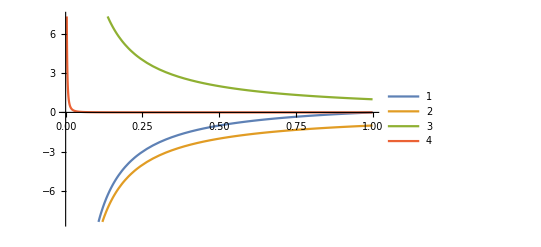

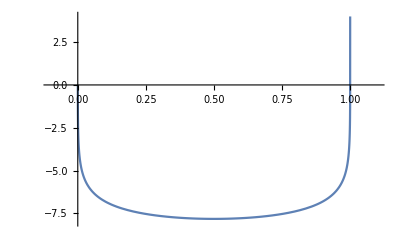

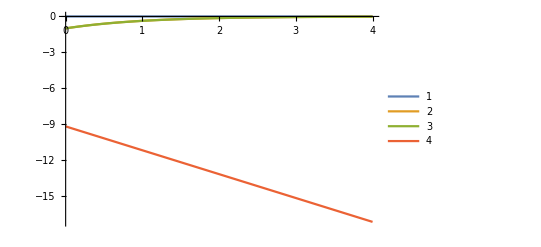

```mathematica
(* influence of overlap for nu=Q *)

plotMeLowerN=igrandN/.eps->10^-15;
plotMeLowerNbar=igrandNbar/.DiracDelta[_]->0/.nu->100M;
plotMeLowerOverlap=igrandOver;
plotMeLowerDiff=plotMeLowerNbar-plotMeLowerOverlap; (* this is "how much of the nbar sector we're allowing to populate our result" *)
Plot[{plotMeLowerN,plotMeLowerNbar,-plotMeLowerOverlap,plotMeLowerDiff},{z,0,1},PlotLegends->Automatic,Background->White]

importanceLowerQ=plotMeLowerDiff/plotMeLowerN;
Plot[Log@-importanceLowerQ,{z,0,1},PlotRange->{{-0.1,1.1},{-8,4}}]

plotMeUpperN=0/.eps->10^-5;
plotMeUpper=igrandNbar/.DiracDelta[_]->0/.nu->100M/.z->Exp[xii];
plotMeUpperOverlap=igrandOver/.z->Exp[xii];
plotMeUpperDiff=plotMeUpper-plotMeUpperOverlap;
Plot[{plotMeUpperN,plotMeUpper,plotMeUpperOverlap,Log@plotMeUpperDiff},{xii,0,4},PlotLegends->Automatic]
```

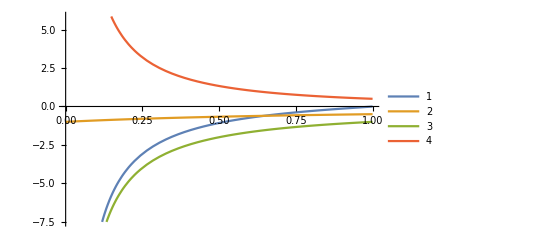

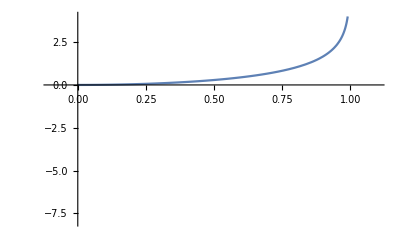

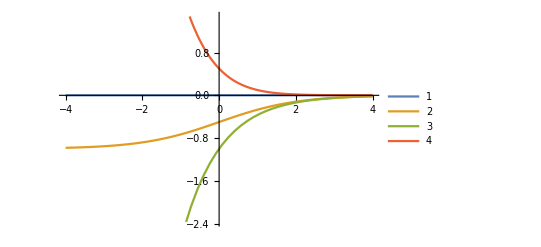

```mathematica
(* influence of overlap for nu=M *)

plotMeLowerN=igrandN/.eps->10^-15;
plotMeLowerNbar=igrandNbar/.DiracDelta[_]->0/.nu->M;
plotMeLowerOverlap=igrandOver;
plotMeLowerDiff=plotMeLowerNbar-plotMeLowerOverlap;
Plot[{igrandN/.eps->10^-1,plotMeLowerNbar,plotMeLowerOverlap,plotMeLowerDiff},{z,0,1},PlotLegends->Automatic,Background->White]

importanceLowerQ=plotMeLowerDiff/plotMeLowerN;
Plot[Log@-importanceLowerQ,{z,0,1},PlotRange->{{-0.1,1.1},{-8,4}}]

plotMeUpperN=0/.eps->10^-5;
plotMeUpperNbar=igrandNbar/.DiracDelta[_]->0/.nu->M/.z->Exp[xii];
plotMeUpperOverlap=igrandOver/.z->Exp[xii];
plotMeUpperDiff=plotMeUpperNbar-plotMeUpperOverlap/.xi->xii;
Plot[{plotMeUpperN,plotMeUpperNbar,plotMeUpperOverlap,plotMeUpperDiff},{xii,-4,4},PlotLegends->Automatic]
```

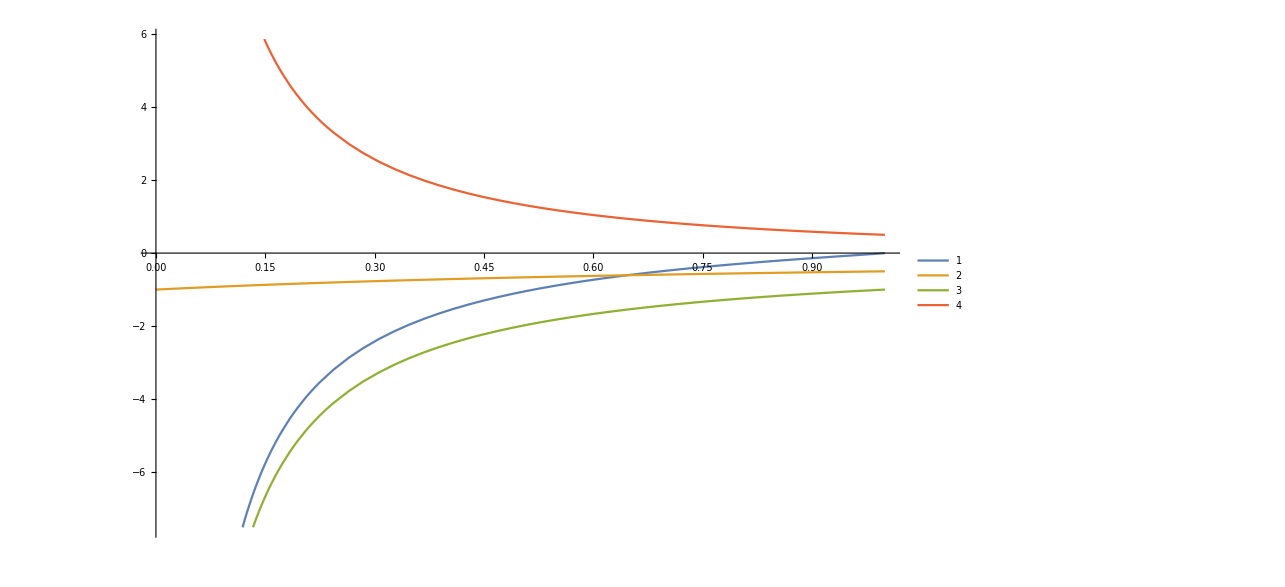

-Graphics-

```mathematica
D[Tan[2x],x]
```

2 sec^2(2 x)

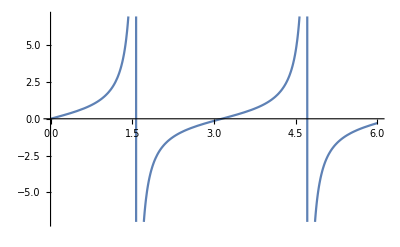

```mathematica
Plot[Tan[x],{x,0,6}]
```

-(ⅇ^etaa ν^2)/(M^2 ((ⅇ^etaa ν^2)/M^2+1))

-1

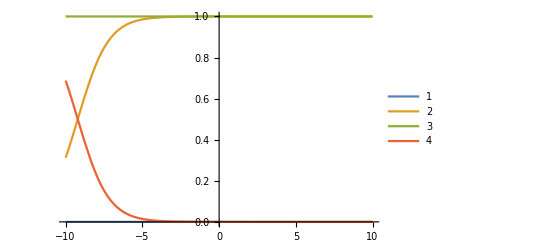

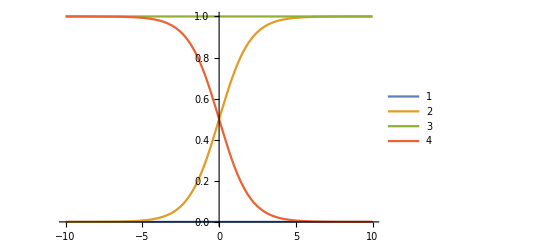

```mathematica
plotMeThetaNbar=igrandNbar*z/.DiracDelta[_]->0/.z->Exp[etaa]
plotMeThetaOverlap=igrandOver*z/.z->Exp[etaa]
plotMeThetaDiff=plotMeThetaNbar-plotMeThetaOverlap;

(* viewing the support of Nbar-overlap in theta space with nu=Q *)
Plot[{0,Abs@plotMeThetaNbar/.nu->100M,Abs@plotMeThetaOverlap/.nu->100M,Abs@plotMeThetaDiff/.nu->100M},{etaa,-10,10},PlotLegends->Automatic]

(* viewing the support of Nbar-overlap in theta space with nu=M*)
Plot[{0,Abs@plotMeThetaNbar/.nu->M,Abs@plotMeThetaOverlap/.nu->M,Abs@plotMeThetaDiff/.nu->M},{etaa,-10,10},PlotLegends->Automatic]
```

```mathematica
2*ArcTan[Exp[-eta]]
%/.eta->-5//N

2*ArcTan[Exp[-eta]]
%/.eta->5//N
```

2 tan^-1(ⅇ^-η)

3.12812

2 tan^-1(ⅇ^-η)

0.0134757